# Mathematical Model for Dual Strain Oscillator (Ye, Kim, Hirning, Josic, Bennett, Science (2015))

## Jae Kyoung Kim

```mathematica
f[x_,y_,a_,b_,nx_,ny_]:=(a+b*x^nx)/(1+x^nx+y^ny);
h[z_,d_,e_,nz_]:=(d+e*z^nz)/(1+z^nz);
g[x_,y_,z_,a_,b_]:=a*x/(b+x+y+z);
s[x_,y_,z_,a_,b_]:=a*x*y/(b+y+z);

(*Simulation Time*)
endt=2000; 

(*Indeterminent parameters*)
{sR,sC,sL,sA,ClpXP,sF,sY}={10.4229,16.4372,8.35996,408.347,683.8944444444445,5.03069,7.72329};

(*Parameters for Promoter Activity*)

{Ro,Rt}=sR*{20.12744975243665,367.47756337340525}; (*Medium: {3.040952115599431,574.965555848093}, Weak:{1.,624.4449954372682}*)
{Co,Ct}=sC*{1.,624.4449954372682};(*Strong: {20.12744975243665,367.47756337340525}, Medium: {3.040952115599431,574.965555848093}*)
{Fo,Ft}=sF*{20.12744975243665,367.47756337340525}; (*Medium: {3.040952115599431,574.965555848093}, Weak:{1.,624.4449954372682}*)
{Yo,Yt}=sY*{1.,1713.8920162816883};(*Medium: {41.800388484046174,197.49124673685773}*)

{Lo,Lt}=sL*{1,1735.4736707426293};
{Ao,At}=sA*{1,5.239201365995503};

{KHw,KHm,KHs}={16599.3838308722,10333.460779349612,5936.867352572741};
{KL,KLt}={47.701842573496464,85.38139408279068};
{KIw,KIm}={2357.295239442264,594.2300264432362};

{nH,nL,nI}={4,2,4};

(*Parameters for Protein Degradation by ClpXP*)
dC=1.8*ClpXP;
KC=1300;

(*Parameters for Singaling Molecules Degradation by AiiA*)
dA=2257;
KA=5110000;

(*Parameters for Diluration Rate*)
d=Log[2]/25;

(*Parameters for Singaling Molecules production*)
Ho=16;
Io=2;

(*Parameters for Singaling Molecules transport*)
DH=3;
DI=126/60;

(*Parameters for Singaling Molecules extracellualr dilution*)
mu=0.1;

(*Parameter for Maturation rate of CFP/YFP*)
m=Log[2]/3;

(*Parameters for Activator and Repressor Fraction*)
da=0.4;
dr=0.4;

(*Time delay*)
tau=7.5;

(*P_2 N_2 topology*)
aone={Ra'[t]==f[Ha[t-tau]/KHs,La[t-tau]/KL,Ro,Rt,nH,nL]-g[Ra[t],Aa[t]+Fa[t]+Ma[t],La[t],dC,KC]-d*Ra[t],Cr'[t]==f[Hr[t-tau]/KHw,Lr[t-tau]/KL,Co,Ct,nH,nL]-g[Cr[t],Ar[t]+Fr[t]+Mr[t],Lr[t],dC,KC]-d*Cr[t],La'[t]==h[Ia[t-tau]/KIw,Lo,Lt,nI]-g[La[t],Aa[t]+Fa[t]+Ma[t],Ra[t],dC,KC]-d*La[t],Lr'[t]==h[Ir[t-tau]/KIw,Lo,Lt,nI]-g[Lr[t],Ar[t]+Fr[t]+Mr[t],Cr[t],dC,KC]-d*Lr[t],Aa'[t]==h[Ia[t-tau]/KIm,Ao,At,nI]-g[Aa[t],La[t]+Fa[t]+Ma[t],Ra[t],dC,KC]-d*Aa[t],Ar'[t]==h[Ir[t-tau]/KIm,Ao,At,nI]-g[Ar[t],Lr[t]+Fr[t]+Mr[t],Cr[t],dC,KC]-d*Ar[t],Ha'[t]==Ho*Ra[t]-s[Aa[t],Ha[t],Ia[t],dA,KA]-d*Ha[t]-DH*(Ha[t]-He[t]),He'[t]==DH*da/(1-da-dr)*(Ha[t]-He[t])-DH*dr/(1-da-dr)*(He[t]-Hr[t])-mu*He[t],Hr'[t]==DH*(He[t]-Hr[t])-s[Ar[t],Hr[t],Ir[t],dA,KA]-d*Hr[t],Ir'[t]==Io*Cr[t]-s[Ar[t],Ir[t],Hr[t],dA,KA]-d*Ir[t]-DI*(Ir[t]-Ie[t]),Ie'[t]==DI*dr/(1-da-dr)*(Ir[t]-Ie[t])-DI*da/(1-da-dr)*(Ie[t]-Ia[t])-mu*Ie[t],Ia'[t]==DI*(Ie[t]-Ia[t])-s[Aa[t],Ia[t],Ha[t],dA,KA]-d*Ia[t],Fa'[t]==f[Ha[t-tau]/KHs,La[t-tau]/KL,Fo,Ft,nH,nL]-g[Fa[t],Aa[t]+Ra[t]+Ma[t],La[t],dC,KC]-(d+m)*Fa[t],Ma'[t]==m*Fa[t]-g[Ma[t],Aa[t]+Ra[t]+Fa[t],La[t],dC,KC]-d*Ma[t],Fr'[t]==f[Ir[t-tau]/KIw,Lr[t-tau]/KL,Yo,Yt,nI,nL]-g[Fr[t],Ar[t]+Cr[t]+Mr[t],Lr[t],dC,KC]-(d+m)*Fr[t],Mr'[t]==m*Fr[t]-g[Mr[t],Ar[t]+Cr[t]+Fr[t],Lr[t],dC,KC]-d*Mr[t]};atwo={Ra[t/;t≤0]==10,Cr[t/;t≤0]==10,La[t/;t≤0]==1,Lr[t/;t≤0]==1,Aa[t/;t≤0]==10,Ar[t/;t≤0]==10,Ha[t/;t≤0]==10,He[t/;t≤0]==10,Hr[t/;t≤0]==10,Ir[t/;t≤0]==10,Ie[t/;t≤0]==10,Ia[t/;t≤0]==10,Fa[t/;t≤0]==10,Ma[t/;t≤0]==10,Fr[t/;t≤0]==10,Mr[t/;t≤0]==10};
mmqt=NDSolve[Join[aone,atwo],{Ra,Cr,La,Lr,Aa,Ar,Ha,He,Hr,Ir,Ie,Ia,Fa,Ma,Fr,Mr},{t,0,endt},MaxSteps->10000000,MaxStepSize->1];

(*P_2 N_1 topology*)
aone={Ra'[t]==f[Ha[t-tau]/KHs,La[t-tau]/KL,Ro,Rt,nH,nL]-g[Ra[t],Aa[t]+Fa[t]+Ma[t],La[t],dC,KC]-d*Ra[t],Cr'[t]==f[Hr[t-tau]/KHw,0,Co,Ct,nH,nL]-g[Cr[t],Ar[t]+Fr[t]+Mr[t],Lr[t],dC,KC]-d*Cr[t],La'[t]==h[Ia[t-tau]/KIw,Lo,Lt,nI]-g[La[t],Aa[t]+Fa[t]+Ma[t],Ra[t],dC,KC]-d*La[t],Lr'[t]==-g[Lr[t],Ar[t]+Fr[t]+Mr[t],Cr[t],dC,KC]-d*Lr[t],Aa'[t]==h[Ia[t-tau]/KIm,Ao,At,nI]-g[Aa[t],La[t]+Fa[t]+Ma[t],Ra[t],dC,KC]-d*Aa[t],Ar'[t]==h[Ir[t-tau]/KIm,Ao,At,nI]-g[Ar[t],Lr[t]+Fr[t]+Mr[t],Cr[t],dC,KC]-d*Ar[t],Ha'[t]==Ho*Ra[t]-s[Aa[t],Ha[t],Ia[t],dA,KA]-d*Ha[t]-DH*(Ha[t]-He[t]),He'[t]==DH*da/(1-da-dr)*(Ha[t]-He[t])-DH*dr/(1-da-dr)*(He[t]-Hr[t])-mu*He[t],Hr'[t]==DH*(He[t]-Hr[t])-s[Ar[t],Hr[t],Ir[t],dA,KA]-d*Hr[t],Ir'[t]==Io*Cr[t]-s[Ar[t],Ir[t],Hr[t],dA,KA]-d*Ir[t]-DI*(Ir[t]-Ie[t]),Ie'[t]==DI*dr/(1-da-dr)*(Ir[t]-Ie[t])-DI*da/(1-da-dr)*(Ie[t]-Ia[t])-mu*Ie[t],Ia'[t]==DI*(Ie[t]-Ia[t])-s[Aa[t],Ia[t],Ha[t],dA,KA]-d*Ia[t],Fa'[t]==f[Ha[t-tau]/KHs,La[t-tau]/KL,Fo,Ft,nH,nL]-g[Fa[t],Aa[t]+Ra[t]+Ma[t],La[t],dC,KC]-(d+m)*Fa[t],Ma'[t]==m*Fa[t]-g[Ma[t],Aa[t]+Ra[t]+Fa[t],La[t],dC,KC]-d*Ma[t],Fr'[t]==f[Ir[t-tau]/KIw,Lr[t-tau]/KL,Yo,Yt,nI,nL]-g[Fr[t],Ar[t]+Cr[t]+Mr[t],Lr[t],dC,KC]-(d+m)*Fr[t],Mr'[t]==m*Fr[t]-g[Mr[t],Ar[t]+Cr[t]+Fr[t],Lr[t],dC,KC]-d*Mr[t]};atwo={Ra[t/;t≤0]==10,Cr[t/;t≤0]==10,La[t/;t≤0]==1,Lr[t/;t≤0]==1,Aa[t/;t≤0]==10,Ar[t/;t≤0]==10,Ha[t/;t≤0]==10,He[t/;t≤0]==10,Hr[t/;t≤0]==10,Ir[t/;t≤0]==10,Ie[t/;t≤0]==10,Ia[t/;t≤0]==10,Fa[t/;t≤0]==10,Ma[t/;t≤0]==10,Fr[t/;t≤0]==10,Mr[t/;t≤0]==10};
mwqt=NDSolve[Join[aone,atwo],{Ra,Cr,La,Lr,Aa,Ar,Ha,He,Hr,Ir,Ie,Ia,Fa,Ma,Fr,Mr},{t,0,endt},MaxSteps->10000000,MaxStepSize->1];

(*Promoter switch to P_lac*)
Ro=177.43812194380044*sR;
Rt=0;
Fo=177.43812194380044*sF;
Ft=0;

(*P_1 N_2 topology*)

aone={Ra'[t]==f[0,La[t-tau]/KLt,Ro,Rt,nH,nL]-g[Ra[t],Aa[t]+Fa[t]+Ma[t],La[t],dC,KC]-d*Ra[t],Cr'[t]==f[Hr[t-tau]/KHw,Lr[t-tau]/KL,Co,Ct,nH,nL]-g[Cr[t],Ar[t]+Fr[t]+Mr[t],Lr[t],dC,KC]-d*Cr[t],La'[t]==h[Ia[t-tau]/KIw,Lo,Lt,nI]-g[La[t],Aa[t]+Fa[t]+Ma[t],Ra[t],dC,KC]-d*La[t],Lr'[t]==h[Ir[t-tau]/KIw,Lo,Lt,nI]-g[Lr[t],Ar[t]+Fr[t]+Mr[t],Cr[t],dC,KC]-d*Lr[t],Aa'[t]==h[Ia[t-tau]/KIm,Ao,At,nI]-g[Aa[t],La[t]+Fa[t]+Ma[t],Ra[t],dC,KC]-d*Aa[t],Ar'[t]==h[Ir[t-tau]/KIm,Ao,At,nI]-g[Ar[t],Lr[t]+Fr[t]+Mr[t],Cr[t],dC,KC]-d*Ar[t],Ha'[t]==Ho*Ra[t]-s[Aa[t],Ha[t],Ia[t],dA,KA]-d*Ha[t]-DH*(Ha[t]-He[t]),He'[t]==DH*da/(1-da-dr)*(Ha[t]-He[t])-DH*dr/(1-da-dr)*(He[t]-Hr[t])-mu*He[t],Hr'[t]==DH*(He[t]-Hr[t])-s[Ar[t],Hr[t],Ir[t],dA,KA]-d*Hr[t],Ir'[t]==Io*Cr[t]-s[Ar[t],Ir[t],Hr[t],dA,KA]-d*Ir[t]-DI*(Ir[t]-Ie[t]),Ie'[t]==DI*dr/(1-da-dr)*(Ir[t]-Ie[t])-DI*da/(1-da-dr)*(Ie[t]-Ia[t])-mu*Ie[t],Ia'[t]==DI*(Ie[t]-Ia[t])-s[Aa[t],Ia[t],Ha[t],dA,KA]-d*Ia[t],Fa'[t]==f[0,La[t-tau]/KLt,Fo,Ft,nH,nL]-g[Fa[t],Aa[t]+Ra[t]+Ma[t],La[t],dC,KC]-(d+m)*Fa[t],Ma'[t]==m*Fa[t]-g[Ma[t],Aa[t]+Ra[t]+Fa[t],La[t],dC,KC]-d*Ma[t],Fr'[t]==f[Ir[t-tau]/KIw,Lr[t-tau]/KL,Yo,Yt,nI,nL]-g[Fr[t],Ar[t]+Cr[t]+Mr[t],Lr[t],dC,KC]-(d+m)*Fr[t],Mr'[t]==m*Fr[t]-g[Mr[t],Ar[t]+Cr[t]+Fr[t],Lr[t],dC,KC]-d*Mr[t]};
atwo={Ra[t/;t≤0]==10,Cr[t/;t≤0]==10,La[t/;t≤0]==1,Lr[t/;t≤0]==1,Aa[t/;t≤0]==10,Ar[t/;t≤0]==10,Ha[t/;t≤0]==10,He[t/;t≤0]==10,Hr[t/;t≤0]==10,Ir[t/;t≤0]==10,Ie[t/;t≤0]==10,Ia[t/;t≤0]==10,Fa[t/;t≤0]==10,Ma[t/;t≤0]==10,Fr[t/;t≤0]==10,Mr[t/;t≤0]==10};
smqt=NDSolve[Join[aone,atwo],{Ra,Cr,La,Lr,Aa,Ar,Ha,He,Hr,Ir,Ie,Ia,Fa,Ma,Fr,Mr},{t,0,endt},MaxSteps->10000000,MaxStepSize->1];

(*P_1 N_1 topology*)
aone={Ra'[t]==f[0,La[t-tau]/KLt,Ro,Rt,nH,nL]-g[Ra[t],Aa[t]+Fa[t]+Ma[t],La[t],dC,KC]-d*Ra[t],Cr'[t]==f[Hr[t-tau]/KHw,0,Co,Ct,nH,nL]-g[Cr[t],Ar[t]+Fr[t]+Mr[t],Lr[t],dC,KC]-d*Cr[t],La'[t]==h[Ia[t-tau]/KIw,Lo,Lt,nI]-g[La[t],Aa[t]+Fa[t]+Ma[t],Ra[t],dC,KC]-d*La[t],Lr'[t]==-g[Lr[t],Ar[t]+Fr[t]+Mr[t],Cr[t],dC,KC]-d*Lr[t],Aa'[t]==h[Ia[t-tau]/KIm,Ao,At,nI]-g[Aa[t],La[t]+Fa[t]+Ma[t],Ra[t],dC,KC]-d*Aa[t],Ar'[t]==h[Ir[t-tau]/KIm,Ao,At,nI]-g[Ar[t],Lr[t]+Fr[t]+Mr[t],Cr[t],dC,KC]-d*Ar[t],Ha'[t]==Ho*Ra[t]-s[Aa[t],Ha[t],Ia[t],dA,KA]-d*Ha[t]-DH*(Ha[t]-He[t]),He'[t]==DH*da/(1-da-dr)*(Ha[t]-He[t])-DH*dr/(1-da-dr)*(He[t]-Hr[t])-mu*He[t],Hr'[t]==DH*(He[t]-Hr[t])-s[Ar[t],Hr[t],Ir[t],dA,KA]-d*Hr[t],Ir'[t]==Io*Cr[t]-s[Ar[t],Ir[t],Hr[t],dA,KA]-d*Ir[t]-DI*(Ir[t]-Ie[t]),Ie'[t]==DI*dr/(1-da-dr)*(Ir[t]-Ie[t])-DI*da/(1-da-dr)*(Ie[t]-Ia[t])-mu*Ie[t],Ia'[t]==DI*(Ie[t]-Ia[t])-s[Aa[t],Ia[t],Ha[t],dA,KA]-d*Ia[t],Fa'[t]==f[0,La[t-tau]/KLt,Fo,Ft,nH,nL]-g[Fa[t],Aa[t]+Ra[t]+Ma[t],La[t],dC,KC]-(d+m)*Fa[t],Ma'[t]==m*Fa[t]-g[Ma[t],Aa[t]+Ra[t]+Fa[t],La[t],dC,KC]-d*Ma[t],Fr'[t]==f[Ir[t-tau]/KIw,Lr[t-tau]/KL,Yo,Yt,nI,nL]-g[Fr[t],Ar[t]+Cr[t]+Mr[t],Lr[t],dC,KC]-(d+m)*Fr[t],Mr'[t]==m*Fr[t]-g[Mr[t],Ar[t]+Cr[t]+Fr[t],Lr[t],dC,KC]-d*Mr[t]};
atwo={Ra[t/;t≤0]==10,Cr[t/;t≤0]==10,La[t/;t≤0]==1,Lr[t/;t≤0]==1,Aa[t/;t≤0]==10,Ar[t/;t≤0]==10,Ha[t/;t≤0]==10,He[t/;t≤0]==10,Hr[t/;t≤0]==10,Ir[t/;t≤0]==10,Ie[t/;t≤0]==10,Ia[t/;t≤0]==10,Fa[t/;t≤0]==10,Ma[t/;t≤0]==10,Fr[t/;t≤0]==10,Mr[t/;t≤0]==10};
swqt=NDSolve[Join[aone,atwo],{Ra,Cr,La,Lr,Aa,Ar,Ha,He,Hr,Ir,Ie,Ia,Fa,Ma,Fr,Mr},{t,0,endt},MaxSteps->10000000,MaxStepSize->1];
```

```mathematica
(*Simulation (Fig. S5)*)
```

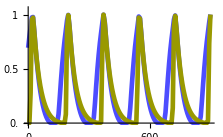

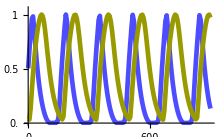

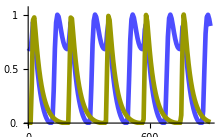

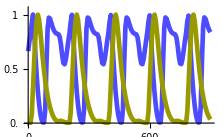

```mathematica
ts=0.02; (*length of thick*)
tp=0.012*1.25;(*Thickness of plot*)
ta=0.006;(*Thickness of axis*)
ft=8*2;(*font size*)
is=72 1.55*2;
xtick={0,300,600,900};
xtickl=xtick;
ytick={0.0,0.25,0.5,0.75,1};
ytickl={0.0,"",0.5,"",1};
endtt=900;

qqt=mmqt;

YY=Table[Mr[t]/.qqt[[1]],{t,endt-1300,endt-1000,6}];
indt=endt-1300+6*(Position[YY,Min[YY]][[1]][[1]]-2);
XX=Table[Ma[t]/.qqt[[1]],{t,indt,indt+endtt,6}];
YY=Table[Mr[t]/.qqt[[1]],{t,indt,indt+endtt,6}];
ListLinePlot[{XX/Max[XX],YY/Max[YY]},DataRange->{0,endtt},PlotRange->{0,1.05},PlotStyle->{{Lighter[Blue,0.3],Thickness[tp]},{Darker[Yellow,0.4],Thickness[tp]}},BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesStyle->Directive[Thickness[ta],FontSize->ft],Ticks->{Table[{xtick[[jj]],xtickl[[jj]],{0,ts}},{jj,1,Length[xtick]}],Table[{ytick[[jj]],ytickl[[jj]],{0,ts}},{jj,1,Length[ytick]}]},ImageSize->is]

qqt=mwqt;
YY=Table[Mr[t]/.qqt[[1]],{t,endt-1300,endt-1000,6}];
indt=endt-1300+6*(Position[YY,Min[YY]][[1]][[1]]-2);
XX=Table[Ma[t]/.qqt[[1]],{t,indt,indt+endtt,6}];
YY=Table[Mr[t]/.qqt[[1]],{t,indt,indt+endtt,6}];
ListLinePlot[{XX/Max[XX],YY/Max[YY]},DataRange->{0,endtt},PlotRange->{0,1.05},PlotStyle->{{Lighter[Blue,0.3],Thickness[tp]},{Darker[Yellow,0.4],Thickness[tp]}},BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesStyle->Directive[Thickness[ta],FontSize->ft],Ticks->{Table[{xtick[[jj]],xtickl[[jj]],{0,ts}},{jj,1,Length[xtick]}],Table[{ytick[[jj]],ytickl[[jj]],{0,ts}},{jj,1,Length[ytick]}]},ImageSize->is]

qqt=smqt;
YY=Table[Mr[t]/.qqt[[1]],{t,endt-1300,endt-1000,6}];
indt=endt-1300+6*(Position[YY,Min[YY]][[1]][[1]]-2);
XX=Table[Ma[t]/.qqt[[1]],{t,indt,indt+endtt,6}];
YY=Table[Mr[t]/.qqt[[1]],{t,indt,indt+endtt,6}];
ListLinePlot[{XX/Max[XX],YY/Max[YY]},DataRange->{0,endtt},PlotRange->{0,1.05},PlotStyle->{{Lighter[Blue,0.3],Thickness[tp]},{Darker[Yellow,0.4],Thickness[tp]}},BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesStyle->Directive[Thickness[ta],FontSize->ft],Ticks->{Table[{xtick[[jj]],xtickl[[jj]],{0,ts}},{jj,1,Length[xtick]}],Table[{ytick[[jj]],ytickl[[jj]],{0,ts}},{jj,1,Length[ytick]}]},ImageSize->is]

qqt=swqt;
YY=Table[Mr[t]/.qqt[[1]],{t,endt-1300,endt-1000,6}];
indt=endt-1300+6*(Position[YY,Min[YY]][[1]][[1]]-2);
XX=Table[Ma[t]/.qqt[[1]],{t,indt,indt+endtt,6}];
YY=Table[Mr[t]/.qqt[[1]],{t,indt,indt+endtt,6}];
ListLinePlot[{XX/Max[XX],YY/Max[YY]},DataRange->{0,endtt},PlotRange->{0,1.05},PlotStyle->{{Lighter[Blue,0.3],Thickness[tp]},{Darker[Yellow,0.4],Thickness[tp]}},BaseStyle->{FontFamily->"Helvetica",FontSize->ft},AxesStyle->Directive[Thickness[ta],FontSize->ft],Ticks->{Table[{xtick[[jj]],xtickl[[jj]],{0,ts}},{jj,1,Length[xtick]}],Table[{ytick[[jj]],ytickl[[jj]],{0,ts}},{jj,1,Length[ytick]}]},ImageSize->is]
```